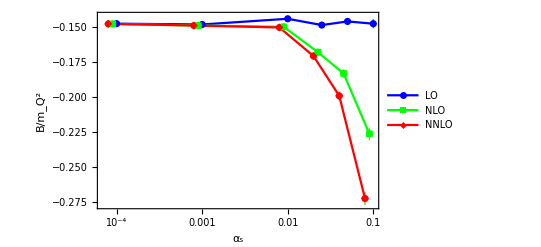

```mathematica
(*First,load the necessary package*)Needs["ErrorBarPlots`"]

(*Define the data*)

dataWithErrors=(*{{-0.147423,0.00329023},{-0.2262,0.00458789},{-0.272446,0.00461639},{-0.116828,0.00250212},{-0.12153,0.00252616},{-0.121815,0.00252694},{-0.118321,0.00306818},{-0.118782,0.00307436},{-0.118785,0.00307439},{-0.119763,0.00329788},{-0.119808,0.00329842},{-0.119809,0.00329842}};*){
{-0.147423,0.00329023},
{-0.2262,0.00458789},
{-0.272446,0.00461639},

{-0.145799,0.00207021},
{-0.18301,0.00301981},
{-0.199035,0.00314879},

{-0.148391,0.0020201},
{-0.167761,0.00224039},
{-0.17055,0.00226572},

{-0.143894,0.00189202},
{-0.149669,0.00179008},
{-0.150114,0.00180009},

{-0.147971,0.00166341},
{-0.148727,0.00164682},
{-0.148732,0.00164688},

{-0.147397,0.00208733},
{-0.14755,0.00210167},
{-0.14755,0.00210167}};

(*Define the x-values for each data point*)

xValues={0.1,0.1*.9,0.1*.8,0.05,0.05*.9,0.05*.8,0.025,0.025*.9,0.025*.8,0.01,0.01*.9,0.01*.8,0.001,0.001*.9,0.001*.8,0.0001,0.0001*.9,0.0001*.8};

(*Transform the data for plotting*)

plotData=Table[{xValues[[i]],Around[dataWithErrors[[i,1]],dataWithErrors[[i,2]]]},{i,Length[dataWithErrors]}];

(*Split the data by LO,NLO,NNLO*)
loData=plotData[[1;;-1;;3]];
nloData=plotData[[2;;-1;;3]];
nnloData=plotData[[3;;-1;;3]];

(*Plot the data with error bars and a log scale for the x-axis*)
ListPlot[{loData,nloData,nnloData},Joined->True,Mesh->All,Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(α\), \(s\)]\)",FontSize->14],Style["\!\(\*FractionBox[\"B\", \(\*SuperscriptBox[\(\*SubscriptBox[\(m\), \(Q\)]\), \(2\)] \*SubscriptBox[\(α\), \(s\)]^2\)]\)",FontSize->14]},GridLines->{xValues,Automatic},GridLinesStyle->Dotted,PlotMarkers->Automatic,PlotRange->All,PlotStyle->{Blue,Green,Red},(*Color scheme for each order*)PlotLegends->{"LO","NLO","NNLO"},Joined->{True,True,True},ScalingFunctions->{"Log","Linear"}]
```

```mathematica
plotData
```

{{0.1,-0.14740.0033},{0.09,-0.2260.005},{0.08,-0.2720.005},{0.05,-0.14580.0021},{0.045,-0.18300.0030},{0.04,-0.19900.0031},{0.025,-0.14840.0020},{0.0225,-0.16780.0022},{0.02,-0.17060.0023},{0.01,-0.14390.0019},{0.009,-0.14970.0018},{0.008,-0.15010.0018},{0.001,-0.14800.0017},{0.0009,-0.14870.0016},{0.0008,-0.14870.0016},{0.0001,-0.14740.0021},{0.00009,-0.14760.0021},{0.00008,-0.14760.0021}}

```mathematica
loData
```

{{0.1,-0.14740.0033},{0.05,-0.14580.0021},{0.025,-0.14840.0020},{0.01,-0.14390.0019},{0.001,-0.14800.0017},{0.0001,-0.14740.0021}}

```mathematica
Dimensions@dataWithErrors
```

{18,2}

```mathematica
Dimensions@xValues
```

{18}

```mathematica
1/4(4/3.)^2
```

0.444444

```mathematica
.12/(2 1/4(4/3)^2)
```

0.135

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
<<MaTeX`
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
colorList={ColorData[97][1],ColorData[97][2],ColorData[97][0]}
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.915, 0.3325, 0.2125]}

```mathematica
OLOlegend=PointLegend[Table[colorList[[ii]],{ii,3}],{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{NNLO}'",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,colorList[[ii]]],{ii,3}],LegendLayout->{"Column",3},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Fig2legend=LineLegend[Table[colorList[[ii]],{ii,3}],{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{NNLO}'",Magnification->0.8]},LegendLayout->{"Column",3},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
loData
```

{{0.1,-0.14740.0033},{0.05,-0.14580.0021},{0.025,-0.14840.0020},{0.01,-0.14390.0019},{0.001,-0.14800.0017},{0.0001,-0.14740.0021}}

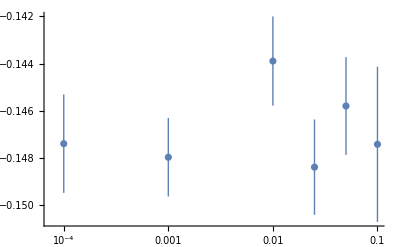

```mathematica
ListLogLinearPlot[{loData,nloData,nnloData}[[1]]]
```

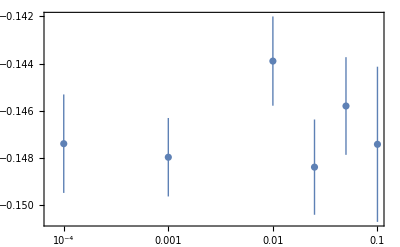

```mathematica
ListLogLinearPlot[{loData,nloData,nnloData}[[1]],Frame->True,IntervalMarkers->"Fences",PlotStyle->{colorList[[1]]},IntervalMarkersStyle->{colorList[[1]]},PlotLegends->If[1==1,Placed[OLOlegend,{0.5,0.1}],None]]
```

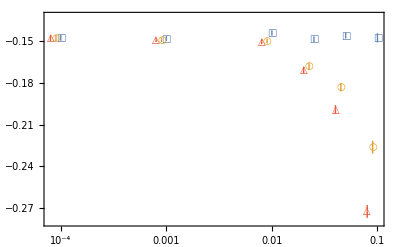

```mathematica
alphaPlot=Show[Table[ListLogLinearPlot[{loData,nloData,nnloData}[[ii]],Frame->True,IntervalMarkers->"Fences",PlotStyle->{colorList[[ii]]},IntervalMarkersStyle->{colorList[[ii]]},PlotLegends->If[ii==1,Placed[OLOlegend,{0.5,0.1}],None]]/.Point[pts_List]:>(Text[Style[markerlist[[ii]],10,Bold],#]&/@pts),{ii,3}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["B_{Q\\overline{Q}Q\\overline{Q}} / m_Q / \\alpha_s^2",Magnification->1.2]},PlotRange->{-.28,-.132}]
```

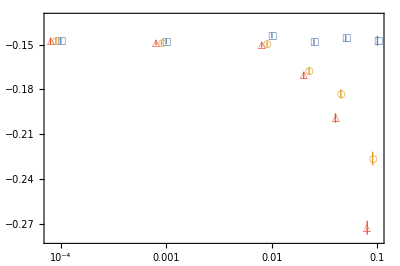

```mathematica
Show[Table[ListLogLinearPlot[{loData,nloData,nnloData}[[ii]],Frame->True,IntervalMarkers->"Fences",PlotStyle->{colorList[[ii]]},IntervalMarkersStyle->{colorList[[ii]]},PlotLegends->If[ii==1,Placed[OLOlegend,{0.5,0.1}],None]]/.Point[pts_List]:>(Text[Style[markerlist[[ii]],10,Bold],#]&/@pts),{ii,3}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["B_{Q\\overline{Q}Q\\overline{Q}} / m_Q / \\alpha_s^2",Magnification->1.2]},PlotRange->{-.28,-.132},AspectRatio->2/3]
```

```mathematica
dataWithErrors[[-1]]
```

{-0.14755,0.00210167}

```mathematica
LOratio=(4/3)^2/4.
```

0.444444

```mathematica
dataWithErrors[[-1]]/(2 LOratio)
```

{-0.165994,0.00236438}

```mathematica
dropboxDir="~/Dropbox (Personal)/";
```

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/alphaPlot.pdf",alphaPlot]
```

~/Dropbox (Personal)//physics/projects/heavy_quark_nuclei/alphaPlot.pdf

```mathematica
widthOverHeight=3/2;
```

```mathematica
figSize=150/widthOverHeight+20
```

120

```mathematica
tab1Size=13+6.5 1 3
```

32.5

```mathematica
tab2Size=13+6.5 6 3
```

130.

```mathematica
mathSize=16(19+9)
```

448

```mathematica
mathSize+figSize+tab1Size+tab2Size
```

730.5

```mathematica
wordSize=3172+359
```

3531

```mathematica
wordSize=3068
```

3068

```mathematica
wordSize+figSize+mathSize+tab1Size+tab2Size
```

3720.5